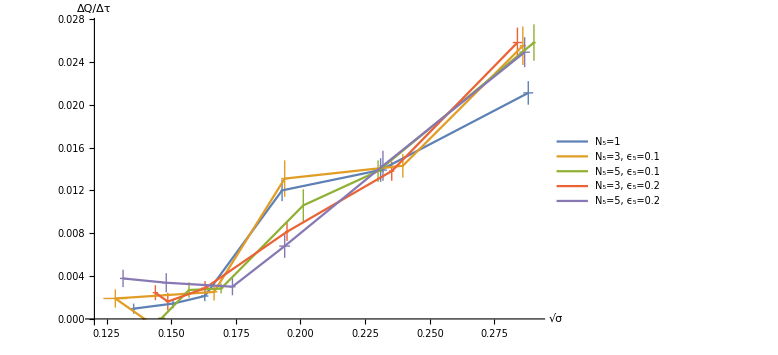

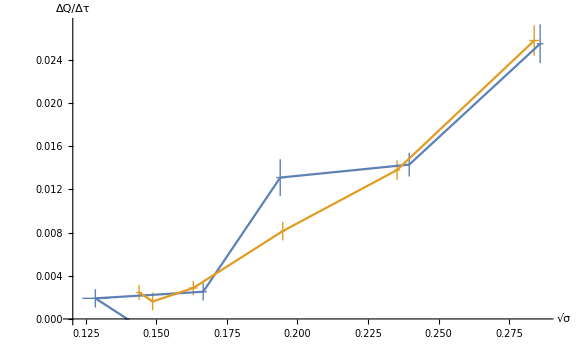

```mathematica
data1={
(*{Around[0.3675,0.0035],Around[0.0298,0.0019]},*)
{Around[0.2881,0.0019],Around[0.0211,0.0011]},
{Around[0.2310,0.0024],Around[0.0139,0.0011]},
{Around[0.1929,0.0006],Around[0.0120,0.0010]},
{Around[0.1630,0.0014],Around[0.00214,0.00048]},
{Around[0.1507,0.0004],Around[0.00143,0.00043]},
{Around[0.1355,0.0010],Around[0.00096,0.00047]}
};
data31={
{Around[0.2860,0.0012],Around[0.0255,0.0018]},
{Around[0.2396,0.0004],Around[0.0143,0.0011]},
{Around[0.1939,0.0014],Around[0.0131,0.0017]},
{Around[0.1666,0.0013],Around[0.00252,0.00080]},
{Around[0.1284,0.0046],Around[0.00191,0.00085]},
{Around[0.1397,0.0008],0}
};
data32={
{Around[0.2839,0.0018],Around[0.0258,0.0014]},
{Around[0.2353,0.0010],Around[0.0138,0.0009]},
{Around[0.1948,0.0008],Around[0.00814,0.00086]},
{Around[0.1631,0.0015],Around[0.00287,0.00066]},
{Around[0.1487,0.0008],Around[0.00162,0.00082]},
{Around[0.1439,0.0010],Around[0.00245,0.00070]}
};
data51={
{Around[0.2903,0.0007],Around[0.0258,0.0017]},
{Around[0.2300,0.0022],Around[0.0138,0.0010]},
{Around[0.2011,0.0003],Around[0.0106,0.0015]},
{Around[0.1693,0.0008],Around[0.00284,0.00046]},
{Around[0.1569,0.0004],Around[0.00270,0.00072]},
{Around[0.1463,0.0013],Around[0.000074,0.000073]}
};
data52={
{Around[0.2867,0.0020],Around[0.0249,0.0014]},
{Around[0.2319,0.0013],Around[0.0143,0.0014]},
{Around[0.1939,0.0021],Around[0.0068,0.0011]},
{Around[0.1737,0.0012],Around[0.00301,0.00080]},
{Around[0.1481,0.0016],Around[0.00338,0.00089]},
{Around[0.1314,0.0012],Around[0.00378,0.00081]}
};
ListPlot[{data1,data31,data51,data32,data52},AxesLabel->{"√σ","ΔQ/Δτ"},PlotRange->{Automatic,{0,Automatic}},PlotLegends->{"N_5=1","N_5=3, ϵ_5=0.1","N_5=5, ϵ_5=0.1","N_5=3, ϵ_5=0.2","N_5=5, ϵ_5=0.2"},ImageSize->Large,Joined->True]
ListPlot[{data31,data32},AxesLabel->{"√σ","ΔQ/Δτ"},PlotRange->{Automatic,{0,Automatic}},ImageSize->Large,Joined->True]
```

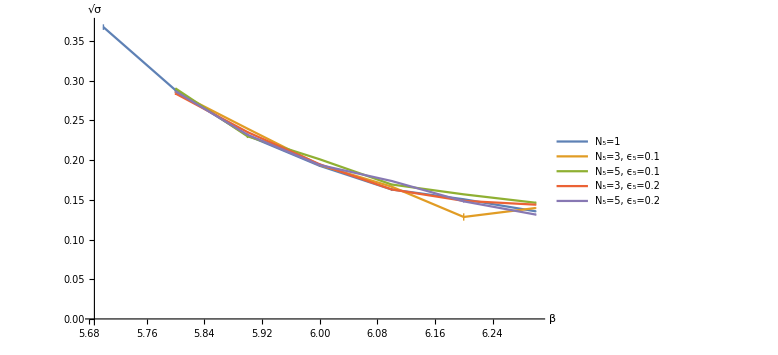

```mathematica
data1={
{5.7,Around[0.3675,0.0035]},
{5.8,Around[0.2881,0.0019]},
{5.9,Around[0.2310,0.0024]},
{6.0,Around[0.1929,0.0006]},
{6.1,Around[0.1630,0.0014]},
{6.2,Around[0.1507,0.0004]},
{6.3,Around[0.1355,0.0010]}
};
data31={
{5.8,Around[0.2860,0.0012]},
{5.9,Around[0.2396,0.0004]},
{6.0,Around[0.1939,0.0014]},
{6.1,Around[0.1666,0.0013]},
{6.2,Around[0.1284,0.0046]},
{6.3,Around[0.1397,0.0008]}
};
data32={
{5.8,Around[0.2839,0.0018]},
{5.9,Around[0.2353,0.0010]},
{6.0,Around[0.1948,0.0008]},
{6.1,Around[0.1631,0.0015]},
{6.2,Around[0.1487,0.0008]},
{6.3,Around[0.1439,0.0010]}
};
data51={
{5.8,Around[0.2903,0.0007]},
{5.9,Around[0.2300,0.0022]},
{6.0,Around[0.2011,0.0003]},
{6.1,Around[0.1693,0.0008]},
{6.2,Around[0.1569,0.0004]},
{6.3,Around[0.1463,0.0013]}
};
data52={
{5.8,Around[0.2867,0.0020]},
{5.9,Around[0.2319,0.0013]},
{6.0,Around[0.1939,0.0021]},
{6.1,Around[0.1737,0.0012]},
{6.2,Around[0.1481,0.0016]},
{6.3,Around[0.1314,0.0012]}
};
ListPlot[{data1,data31,data51,data32,data52},AxesLabel->{"β","√σ"},PlotRange->{Automatic,Automatic},PlotLegends->{"N_5=1","N_5=3, ϵ_5=0.1","N_5=5, ϵ_5=0.1","N_5=3, ϵ_5=0.2","N_5=5, ϵ_5=0.2"},ImageSize->Large,Joined->True]
```